```mathematica
n=10000000;
X=RandomVariate[NormalDistribution[1.,.1],n];
Y=RandomVariate[NormalDistribution[1.,.01],n];
μ=Mean[X/Y];
σ=StandardDeviation[X/Y];
a=Min[X/Y];
b=Max[X/Y];
Show[
Histogram[{X/Y},200,"PDF"],
Plot[PDF[NormalDistribution[μ,σ],x],{x,a,b},PlotRange->All]
]
```

```mathematica
Exit
```

```mathematica
(*Delete all compiled dynamic libraries of the CycleSamplerLink package.*)
If[
FileExistsQ[#],DeleteDirectory[#,DeleteContents->True]
]&[FileNameJoin[{ParentDirectory[NotebookDirectory[]],"LibraryResources",$SystemID}]]
```

```mathematica
Get[
FileNameJoin[{ParentDirectory[NotebookDirectory[]],"CycleSamplerLink.m"}]
]
```

```mathematica
d=3;
r=ConstantArray[1.,8];
n=10000;(*Number of samples we use for one sample of the weighted mean.*)
m=10000;(*Number of weighted means.*)
chunkCount=10;
{X,Y}=Transpose[Join@@Transpose[Table[
Block[{data,x,ω},
data=CycleSampleChordLength[d, r, {0,4},m n/chunkCount,
"QuotientSpace" -> True,
"SphereRadii"->"SymplecticQuotient"
];
(*Now we have m samples of the weighted mean, stored in S:*)
x=Partition[data[[2,1]],n];
ω=Partition[data[[2,2]],n];
{Total[x ω,{2}],Total[ω,{2}]}
]
,{chunkCount}],{1,3,2}]];//AbsoluteTiming

T=X/Y;

μT=Mean[T];
σT=StandardDeviation[T];
a=Quantile[T,0.001];
b=Quantile[T,0.999];
Show[
Histogram[T,"Wand","PDF"],
Plot[PDF[NormalDistribution[μT,σT],x],{x,a,b},PlotRange->All],
PlotRange->{{a,b},{0,All}}
]
```

Compiling cSampleChordLength[3]...

Reading build settings from /Users/Henrik/github/CycleSamplerLink/LibraryResources/Source/BuildSettings.m

Compilation done. Time elapsed = 2.77006 s.

$Aborted

$Aborted

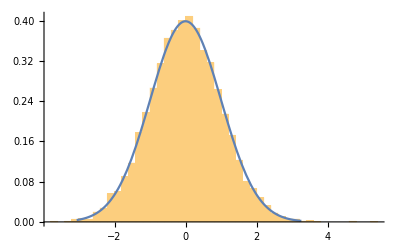

0.782473

```mathematica
meanX=Mean[X];
varX=Variance[X];
meanY=Mean[Y];
varY=Variance[Y];
covXY=Covariance[X,Y];
Geary=T↦(meanY T-meanX)/Sqrt[varY T^2-2 covXY T+varX];

t=Geary[T];
μt=Mean[t];
σt=StandardDeviation[t];
a=Quantile[t,0.001];
b=Quantile[t,0.999];
Show[
Histogram[t,"Wand","PDF"],
Plot[PDF[NormalDistribution[0,1],x],{x,a,b},PlotRange->All],
PlotRange->{{a,b},{0,All}}
]
```

```mathematica
Correlation[X,Y]
```

0.819838

```mathematica
t=.
```

```mathematica
T=.
r=.
```

```mathematica
PDF[NormalDistribution[0,1],z]
```

(ⅇ^(-z^2/2))/(√(2 π))

```mathematica
(D[Erf[t/Sqrt[2]],t]/.t->T+r)-(D[Erf[t/Sqrt[2]],t]/.t->T-r)
```

-ⅇ^(-1/2 (-r+T)^2) √(2/π)+ⅇ^(-1/2 (r+T)^2) √(2/π)

```mathematica
?Geary
```

```mathematica
meanX=.;
varX=.;
meanY=.;
varY=.;
covXY=.;
GearyTransform=T↦(meanY T-meanX)/Sqrt[varY T^2-2 covXY T+varX];
```

```mathematica
F=r↦Erf[GearyTransform[T+r]/Sqrt[2]]-Erf[GearyTransform[T-r]/Sqrt[2]]
```

Function[r,Erf[GearyTransform[T+r]/(√2)]-Erf[GearyTransform[T-r]/(√2)]]

```mathematica
F'[r]//FullSimplify
```

√(2/π) ((ⅇ^(-(meanX+meanY (r-T))^2/(2 (2 covXY (r-T)+varX+(r-T)^2 varY))) (-covXY (meanX+meanY (-r+T))+meanY varX+meanX (-r+T) varY))/((2 covXY (r-T)+varX+(r-T)^2 varY)^(3/2))+(ⅇ^((meanX-meanY (r+T))^2/(4 covXY (r+T)-2 (varX+(r+T)^2 varY))) (-covXY (meanX+meanY (r+T))+meanY varX+meanX (r+T) varY))/((-2 covXY (r+T)+varX+(r+T)^2 varY)^(3/2)))

```mathematica
D[GearyTransform[T],T]
```

-((-meanX+meanY T) (-2 covXY+2 T varY))/(2 (-2 covXY T+varX+T^2 varY)^(3/2))+meanY/(√(-2 covXY T+varX+T^2 varY))

```mathematica
(GearyTransform[T]-confidence)/D[GearyTransform[T],T]//Simplify
```

((-2 covXY T+varX+T^2 varY) (meanX-meanY T+confidence √(-2 covXY T+varX+T^2 varY)))/(covXY (meanX+meanY T)-meanY varX-meanX T varY)

```mathematica
Solve[t==GearyTransform[T],T]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{T→(meanX meanY-covXY t^2-√(-2 covXY meanX meanY t^2+covXY^2 t^4+meanY^2 t^2 varX+meanX^2 t^2 varY-t^4 varX varY))/(meanY^2-t^2 varY)},{T→(meanX meanY-covXY t^2+√(-2 covXY meanX meanY t^2+covXY^2 t^4+meanY^2 t^2 varX+meanX^2 t^2 varY-t^4 varX varY))/(meanY^2-t^2 varY)}}

```mathematica
Exit
```

```mathematica
(*Delete all compiled dynamic libraries of the CycleSamplerLink package.*)
If[
FileExistsQ[#],DeleteDirectory[#,DeleteContents->True]
]&[FileNameJoin[{ParentDirectory[NotebookDirectory[]],"LibraryResources",$SystemID}]]

Get[
FileNameJoin[{ParentDirectory[NotebookDirectory[]],"CycleSamplerLink.m"}]
]

cf=CycleSamplerLink`Private`cConfidenceSampleRandomVariable[3]

cf=CycleSamplerLink`Private`cSampleRandomVariable[3]
```

Compiling cConfidenceSampleRandomVariable[3]...

Reading build settings from /Users/Henrik/github/CycleSamplerLink/LibraryResources/Source/BuildSettings.m

Compilation done. Time elapsed = 3.14997 s.

LibraryFunction[…]

Compiling cSampleRandomVariable[3]...

Compilation done. Time elapsed = 2.60407 s.

LibraryFunction[…]

```mathematica
d=3;
r=ConstantArray[1.,16];
data=CycleConfidenceSample["Gyradius",d,r,0.01,
"ConfidenceLevel"->0.95,
"ThreadCount"->8,
"MaxSamples"->100000000,
"ChunkSize"->1000000
];

Dataset[data]
```

Profile will be written to /Users/Henrik/Tools_Profile.tsv.

Log     will be written to /Users/Henrik/Tools_Log.txt.

dimension        = 3

edge_count       = 16

fun_count        = 1

thread_count     = 8

confidence level = 0.95

ConfidenceSample works on the following random variables:

Gyradius

N = 1000000

current confidence of Gyradius = 0.2397229881074772

N = 2000000

current confidence of Gyradius = 0.3338452138940425

N = 3000000

current confidence of Gyradius = 0.4027699862285435

N = 4000000

current confidence of Gyradius = 0.4582029937182618

N = 5000000

current confidence of Gyradius = 0.5048153476400417

N = 6000000

current confidence of Gyradius = 0.5450792864751319

N = 7000000

current confidence of Gyradius = 0.5804056770935414

N = 8000000

current confidence of Gyradius = 0.6117978836569193

N = 9000000

current confidence of Gyradius = 0.6399586949174818

N = 10000000

current confidence of Gyradius = 0.6653290584406164

N = 11000000

current confidence of Gyradius = 0.6883908490829381

N = 12000000

current confidence of Gyradius = 0.7094065609107876

N = 13000000

current confidence of Gyradius = 0.7286409179290276

N = 14000000

current confidence of Gyradius = 0.7463242512228041

N = 15000000

current confidence of Gyradius = 0.7626145682076584

N = 16000000

current confidence of Gyradius = 0.7776595142153391

N = 17000000

current confidence of Gyradius = 0.7915526305627167

N = 18000000

current confidence of Gyradius = 0.8044440473149486

N = 19000000

current confidence of Gyradius = 0.8164190933967155

N = 20000000

current confidence of Gyradius = 0.8275344292723497

N = 21000000

current confidence of Gyradius = 0.8378897434628301

N = 22000000

current confidence of Gyradius = 0.8475422828261344

N = 23000000

current confidence of Gyradius = 0.8565449311882158

N = 24000000

current confidence of Gyradius = 0.8649608691065025

N = 25000000

current confidence of Gyradius = 0.8728249178489775

N = 26000000

current confidence of Gyradius = 0.880186758041317

N = 27000000

current confidence of Gyradius = 0.8870733891241545

N = 28000000

current confidence of Gyradius = 0.893537813255834

N = 29000000

current confidence of Gyradius = 0.8995962076846299

N = 30000000

current confidence of Gyradius = 0.9052823987415766

N = 31000000

current confidence of Gyradius = 0.9106213407632278

N = 32000000

current confidence of Gyradius = 0.9156347858020613

N = 33000000

current confidence of Gyradius = 0.9203351484755083

N = 34000000

current confidence of Gyradius = 0.9247619856481907

N = 35000000

current confidence of Gyradius = 0.9289214810028974

N = 36000000

current confidence of Gyradius = 0.9328383547378785

N = 37000000

current confidence of Gyradius = 0.9365285410290837

N = 38000000

current confidence of Gyradius = 0.9399988764382383

N = 39000000

current confidence of Gyradius = 0.9432679260708563

N = 40000000

current confidence of Gyradius = 0.9463471740687122

N = 41000000

current confidence of Gyradius = 0.9492518051564567

N = 42000000

current confidence of Gyradius = 0.9519907938456428

N = 42000000

Gyradius

failure = 0.001990793845642824

Dfailure = 22.33762996463567

failure = -3.498420533076807e-05

means[i] = 1.176589605834201

errors[i] = 0.009910877123097007

```mathematica
Dataset[data]
```

```mathematica
CycleSample["DiagonalLength",d,r,10000000]//AbsoluteTiming
```

{1.47962,WeightedData[<<10000000>>]}